```mathematica
ClearAll["Global1*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
(*The Following Analysis is incorrect. The reason is 2 fold. 
1. We extended the Fermi liquid phase into the region SC region in order to measure Δη which is not correct. Infact the small latent heat (atleast in comparison to the stress vs Transition temperature plot used here) that we think we get makes sense from the point of view of the transformation being a second order Phase Transformation, ie, the entropy is continuous.
2. Since we are assuming that it is a 1st Order phase Transition, we should expect to see a smeared out delta function near the transition temperature. This represents the latent heat that absorbed/released during the phase transition. Check the overleaf file "Superconductivity/ThermoMechanics General Results/What to expect/Specific heat for different phase Transitions/1st Order PhaseTransformation".*)
```

```mathematica
(*Data 1*)
```

```mathematica
(*Extracting C_s and C_n from the above graph. The 2 corresponds to data set 2.*)
TvsCs1:={{0.5199633240201718,32.88428324697755},{0.544065670763881,34.12780656303973},{0.5721816153001116,35.509499136442145},{0.6002940998382451,36.82210708117444},{0.626403245478215,38.13471502590674},{0.6585397078031607,39.792746113989644},{0.6886693712318458,41.38169257340242},{0.7227503524873061,41.86528497409327},{0.7588865726123851,43.38514680483593},{0.795078152707016,46.010362694300525},{0.8352141306322282,47.39205526770294},{0.8733536896554707,48.9119170984456},{0.917489425380816,50.15544041450778},{0.9616839810738104,52.57340241796201},{1.0118228134974527,53.678756476683944},{1.055986229207574,55.47495682210709},{1.1101524994161254,56.994818652849744},{1.1643187696246768,58.51468048359241},{1.2225055576219432,60.31088082901555},{1.2806646656344343,61.554404145077726},{1.3448303303433184,62.72884283246978},{1.412936932884687,62.59067357512954},{1.492291989239406,47.046632124352335},{1.5560632141652322,40.34542314335061},{1.6221872377970195,40.62176165803109},{1.700303614833012,40.34542314335061},{1.772420355168805,40.27633851468049},{1.8445440155007917,40.34542314335061},{1.91865025474236,40},{1.9927980139610926,40.48359240069085}}
TvsCn1:={{0.5183302049183872,40.27633851468049},{0.5303502383073689,40.27633851468049},{0.5624036606779865,40.27633851468049},{0.5824370496596226,40.27633851468049},{0.5944570830486043,40.27633851468049},{0.6084804553357496,40.27633851468049},{0.6325205221137128,40.27633851468049},{0.6485472332990216,40.27633851468049},{0.672587300076985,40.27633851468049},{0.7006375046493724,40.34542314335061},{0.7246741114292387,40.27633851468049},{0.7487141782072019,40.27633851468049},{0.7807676005778196,40.27633851468049},{0.8008009895594557,40.27633851468049},{0.8208343785410918,40.27633851468049},{0.8468777842172186,40.27633851468049},{0.8789312065878363,40.27633851468049},{0.9129879678566176,40.27633851468049},{0.9390313735327445,40.27633851468049},{0.9670781181070349,40.27633851468049},{0.9931215237831619,40.27633851468049},{1.0271782850519433,40.27633851468049},{1.0412016573390885,40.27633851468049},{1.0632383852188882,40.27633851468049},{1.0952918075895057,40.27633851468049},{1.1213386732637298,40.34542314335061},{1.1433719411454324,40.27633851468049},{1.1774287024142136,40.27633851468049},{1.2134888025811585,40.27633851468049},{1.237528869359122,40.27633851468049},{1.277599107320491,40.34542314335061},{1.3056423918966846,40.27633851468049},{1.343705830961793,40.27633851468049},{1.379765931128738,40.27633851468049},{1.4078126757030285,40.27633851468049},{1.44186943697181,40.27633851468049},{1.4679128426479366,40.27633851468049},{1.4999662650185543,40.27633851468049},{1.5400330429818265,40.27633851468049},{1.5780964820469352,40.27633851468049},{1.6061432266212257,40.27633851468049},{1.6381966489918434,40.27633851468049},{1.66424005466797,40.27633851468049},{1.700300154834915,40.27633851468049},{1.7283468994092055,40.27633851468049},{1.7543903050853324,40.27633851468049},{1.7984637608449319,40.27633851468049},{1.8245071665210588,40.27633851468049},{1.8465438944008583,40.27633851468049},{1.8705874211769185,40.34542314335061},{1.8986307057531122,40.27633851468049},{1.918660634736651,40.20725388601036},{1.9427041615127114,40.27633851468049},{1.9747575838833291,40.27633851468049},{2.0028043284576196,40.27633851468049}}
```

```mathematica
K=(5.75*10^3)/(340.3076*10^-3)*10^-3;(*(density in kg/m^3)/(au in kg/mol)*(Subscript[c, mol] in J/mol/K^2), the last 10^-3 is to convert form mJ to J for Subscript[c, mol]. Multiplying this to Cmol gives us [Δη]=J/(m^3 K)*)
Ts1=Range[Length[TvsCs1]];
Cs1=Range[Length[TvsCs1]];
For[i=1,i<=Length[TvsCs1],i++,Ts1[[i]]=TvsCs1[[i]][[1]];Cs1[[i]]=K*TvsCs1[[i]][[2]]]
{Length[Ts1],Length[Cs1]};
Ts1;
Cs1;
Tn1=Range[Length[TvsCn1]];
Cn1=Range[Length[TvsCn1]];
For[i=1,i<=Length[TvsCn1],i++,Tn1[[i]]=TvsCn1[[i]][[1]];Cn1[[i]]=K*TvsCn1[[i]][[2]]]
{Length[Tn1],Length[Cn1]};
Tn1;
Cn1;
```

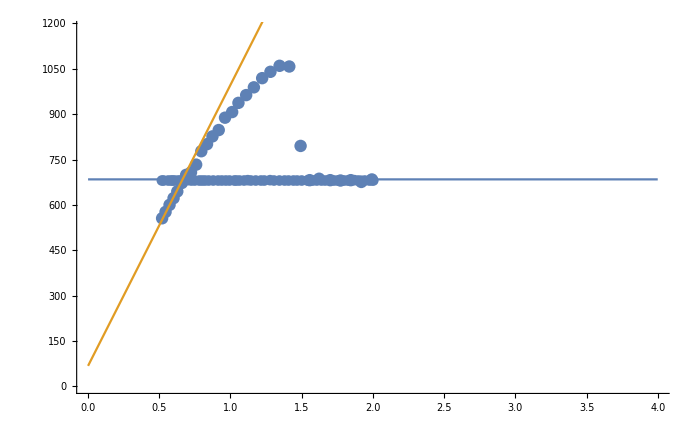

```mathematica
plt11=ListPlot[Transpose@{Ts1,Cs1}];(*Cs vs temp*)
plt12=ListPlot[Transpose@{Tn1,Cn1}];(*Cn vs temp*)
plt13=Plot[{K*40.5,K*(55x+4)},{x,0,4}];
Show[plt11,plt12,plt13,PlotRange->{0,K*70},AxesOrigin->Automatic](*{1.58,37.9}*)
```

```mathematica
Δη1=0;
CpOnset1 = 1.55 ;(*From the curve fitting above*)
m1=K*55;(*fitting the linear extrapolation*)
c1=K*4;(*from fitting the linear extrapolation*)
cn1=K*40.5;(*Fitting the linear interpolation to the normal state*)
y1=Range[Length[Ts1]];
```

```mathematica
For[i=1,i<=Length[y1],i++,y1[[i]]=(cn1-Cs1[[i]])](*storing the integrand as values of y.*)
For[i=1,Ts1[[i]]<=CpOnset1,i++,Δη1+=(Ts1[[i+1]]-Ts1[[i]])*((y1[[i]]+y1[[i+1]])/2)](*The Discrete sum*)
Δη1(*The units are J/m^3/K*)
Δη1+=Integrate[cn1-(m1*x+c1),{x,0,Ts1[[1]]}](*c>=0, thus first term*)
```

-180.442

14.6064

```mathematica
(cn1+cn1-Cs1[[1]])/2*Ts1[[1]]-180(*Testing the second integral using Order of magnitude analysis*)
```

31.3615

```mathematica
(*The approximation to dσ/dθ*(Subscript[ϵ, s]-Subscript[ϵ, n]) is as follows*)
Subscript[Δσ, c]=(0.25+0.03125)*10^6;(*Computing values from the curve*)
Δθ=0.125*9/5; (*Approximating from discrete curve*)
Subscript[Δσ, c]/Δθ*(0.57/100)
```

7125.

```mathematica
(*The  LHS and the RHS of the Clausius Clayperon equation don't match.*)
```

# Data2

```mathematica
-Graphics-
(*The theory of the Following has been laid out in sro-pt-6.nb. Note that unlike the above, this is just the electronic contribution to the specific heat. It behaves the same way as that laid out by the BCS theory. Moreover we are in the range of 1.5K which is lower than √γ/β~14K implying that the electroninc contribution is more than the phonon contribution. We assume that in the SC phase the phonon contribution doesnt matter.*)
```

```mathematica
(*Extracting C_s and C_n from the above graph. The 2 corresponds to data set 2.*)TvsCs2:={{0.12521550525554703,6.3025786478319645},{0.15298555883061682,7.368889383237857},{0.16700035222364318,8.654691062788501},{0.20185195484122098,10.793986244739813},{0.22977031310828067,12.720464193685928},{0.25761451902934507,14.216858535861931},{0.29239196930092826,15.926070111043131},{0.31334000704447273,17.424689023598972},{0.34118421296553736,18.92108336577499},{0.3759245870641226,20.415253137571142},{0.40380586915818517,22.126689283132194},{0.438657471775763,24.26598446508352},{0.47343492204734616,25.97519604026472},{0.5081752961459314,27.46936581206087},{0.5499972192870244,30.036520030402457},{0.5848117457316051,31.960773408968734},{0.6266336688726986,34.527927627310305},{0.6821366998498415,36.44550729473703},{0.7169512262944213,38.369760673303304},{0.7586989970895197,40.50683128487478},{0.7934022950151083,41.78595925328587},{0.8212835771091704,43.49739539884693},{0.8420833101607248,44.13584709786255},{0.8699275160817899,45.632241440038555},{0.904630814007378,46.911369408449644},{0.9393341119329661,48.19049737686075},{0.9739632575125592,49.039541738501754},{1.0017703872606267,50.320894277292695},{1.0504143262332462,52.455740318484324},{1.0851547003318314,53.94991009028047},{1.15452422001001,56.29312422371762},{1.216886342991676,57.99343751737944},{1.2585970376137774,59.91546632556587},{1.314174220936915,62.2631295997627},{1.3488404426895055,63.32721576478875},{1.3972619246241402,64.17181098567005},{1.4383423243052849,62.43812913631054},{1.4378232578833212,59.42754388891978},{1.4650000926904325,57.05318577016479},{1.4646293309604586,54.902767736314246},{1.4642956454034817,52.96739150584875},{1.4845392358600744,50.380216154088565},{1.4909163376156314,47.367406336317956},{1.504300836067701,44.99749735832266},{1.5106779378232575,41.984687540552045},{1.5172404204438021,40.047086739706714},{1.5378176964573718,39.39528761841201},{1.5514988042934208,38.74571306749715},{1.5651799121294703,38.096138516582315},{1.592764584839553,38.087240235062936},{1.641037762082198,38.071668242404016},{1.716895612034926,38.04719796822572},{1.7376953450864803,38.68564966724132},{1.77884989711362,37.382051424651934},{1.8132565856552283,36.94084496598259},{1.8754333277719075,37.56594924271916},{1.92374358118755,37.765419053445285},{1.9927052629627573,37.743173349646824}}
TvsCn2:={{-0.0003614926867254731,37.95599058265206},{0.04101551637839873,37.942643160372995},{0.08928869362104352,37.927071167714075},{0.12380661068164467,38.13099011919991},{0.185835048106334,37.895927182396235},{0.22035296516693514,38.09984613388207},{0.26862614240958016,38.08427414122315},{0.31689931965222495,38.06870214856423},{0.3582763287173494,38.05535472628516},{0.39275716960495277,38.04423187438593},{0.4410303468475978,38.02865988172701},{0.509992028622805,38.00641417792856},{0.5789537103980122,37.9841684741301},{0.644467308084459,37.96303505552157},{0.6892924012383435,37.94857534805257},{0.7582540830135507,37.926329644254125},{0.7996125539921768,37.80546132028252},{0.8548004374988407,37.895185658936285},{0.9237621192740479,37.872939955137824},{0.978931464694214,37.855143392099066},{1.0203084737593384,37.84179596982},{1.0478931464694212,37.832897688300605},{1.0823739873570246,37.82177483640139},{1.123750996422149,37.808427414122306},{1.1789203418423146,37.79063085108355},{1.206505014552398,37.78173256956417},{1.2410229316129988,37.98565152104999},{1.261674359972563,37.7639360065254},{1.3237398735702501,37.74391487310679},{1.3444283781028123,37.73724116196726},{1.3720130508128952,37.72834288044787},{1.3995977235229775,37.71944459892849},{1.4271823962330608,37.71054631740911},{1.4685594052981847,37.69719889513004},{1.5099734905363067,37.89889327623601},{1.5582466677789517,37.88332128357709},{1.627208349554159,37.86107557977864},{1.682377694974325,37.84327901673987},{1.73065087221697,37.82770702408095},{1.7996496301651748,38.02050312366757},{1.8340933948797806,37.79433846838327},{1.9030550766549879,37.772092764584826},{1.9720167584301946,37.749847060786365}}
```

```mathematica
K=(5.75*10^3)/(340.3076*10^-3)*10^-3;(*(density in kg/m^3)/(au in kg/mol)*(Subscript[c, mol] in J/mol/K^2), the last 10^-3 is to convert form mJ to J for Subscript[c, mol]. Multiplying this to Cmol gives us [Δη]=J/(m^3 K)*)
Ts2=Range[Length[TvsCs2]];
Cs2=Range[Length[TvsCs2]];
For[i=1,i<=Length[TvsCs2],i++,Ts2[[i]]=TvsCs2[[i]][[1]];Cs2[[i]]=K*TvsCs2[[i]][[2]]]
{Length[Ts2],Length[Cs2]};
Ts2;
Cs2;
Tn2=Range[Length[TvsCn2]];
Cn2=Range[Length[TvsCn2]];
For[i=1,i<=Length[TvsCn2],i++,Tn2[[i]]=TvsCn2[[i]][[1]];Cn2[[i]]=K*TvsCn2[[i]][[2]]]
{Length[Tn2],Length[Cn2]};
Tn2;
Cn2;
```

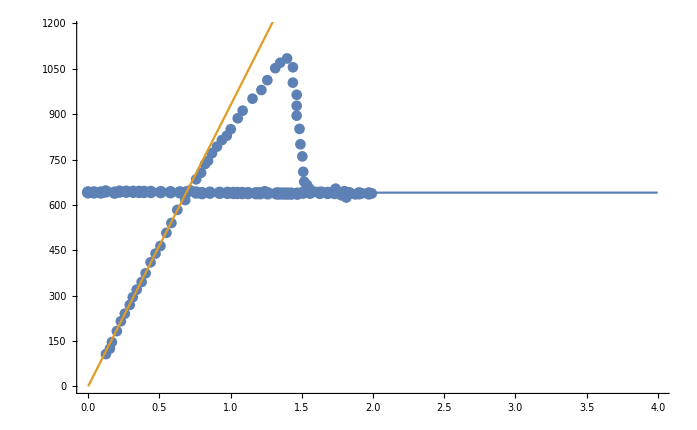

```mathematica
plt21=ListPlot[Transpose@{Ts2,Cs2}];(*Cs vs temp*)
plt22=ListPlot[Transpose@{Tn2,Cn2}];(*Cn vs temp*)
plt23=Plot[{K*37.9,K*55x},{x,0,4}];
Show[plt21,plt22,plt23,PlotRange->{0,K*70},AxesOrigin->Automatic](*{1.58,37.9}*)
```

```mathematica
Δη2=0;
CpOnset2 = 1.58 ;(*From the curve fitting above*)
m2=K*55;(*fitting the linear extrapolation*)
c2=0;(*from fitting the linear extrapolation*)
cn2=K*37.9;(*Fitting the linear interpolation to the normal state*)
y2=Range[Length[Ts2]];
```

```mathematica
For[i=1,i<=Length[y2],i++,y2[[i]]=(cn2-Cs2[[i]])](*storing the integrand as values of y.*)
For[i=1,Ts2[[i]]<=CpOnset2,i++,Δη2+=(Ts2[[i+1]]-Ts2[[i]])*((y2[[i]]+y2[[i+1]])/2)](*The Discrete sum*)
Δη2(*The units are J/m^3/K*)
Δη2+=Integrate[cn2-(m2*x+c2),{x,0,Ts2[[1]]}](*c>=0, thus first term*)
(*The reason this doesnt match the jump in entropy calculation above is because this is a plot fo the electronic specific heat while the above is a plot of the total specific heat capacity. However it doesnt make sense that the above (which accounts for the phonons) would have a smaller jump in entropy!!!*)
```

-52.3224

20.5774

```mathematica
(cn2+cn2-Cs2[[1]])/2*Ts2[[1]]-52.3224(*Testing the second integral using Order of magnitude analysis*)
```

21.1955

```mathematica
(*The approximation to dσ/dθ*(Subscript[ϵ, s]-Subscript[ϵ, n]) is as follows*)
Subscript[Δσ, c]=(0.25+0.03125)*10^6;(*Computing values from the curve*)
Δθ=0.125*9/5; (*Approximating from discrete curve*)
Subscript[Δσ, c]/Δθ*(0.57/100)
```

7125.

```mathematica
(*The  LHS and the RHS of the Clausius Clayperon equation don't match.*)
```